```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
(*
``type-1 --- TrX1^2;
``type-2 --- TrX1X2;
``type-3 --- TrXiXi;
*)
$K = 9;
Do[
data1[$N] = ToExpression@Import["../../../runs/Moments/type-1/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
data2[$N] = ToExpression@Import["../../../runs/Moments/type-2/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
data3[$N] = ToExpression@Import["../../../runs/Moments/type-3/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
, {$N, 4, 9}];
```

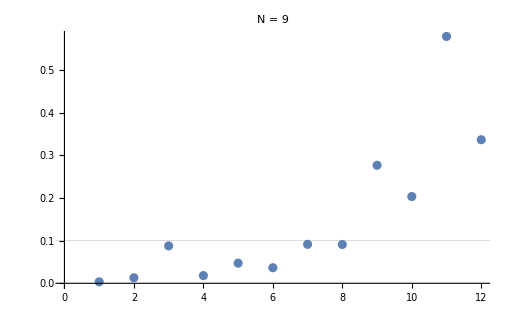

```mathematica
With[{$N = 9}, ListPlot[((#["Uncertainty"])/(#["Value"]))&/@Around/@(data1[$N][[All, 2;;]]ᵀ),
GridLines->{None, {0.1}},
PlotLabel->"N = "<>ToString@$N
]]
```

```mathematica
a = RandomComplex[{-1, 1}, {1000, 1000}];
b = RandomComplex[{-1, 1}, {1000, 1000}];
```

```mathematica
Sum[x[1, a]*x[1, a], {a, 1, ($N)^2-1}]
```

```mathematica
f[e, a, b]f[e, c, d]x[i, a]x[j, b]x[i, c]x[j, d]
```

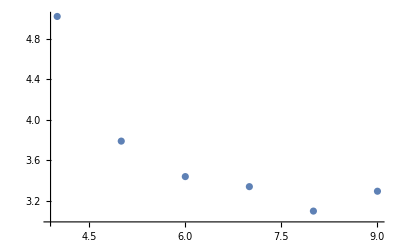

```mathematica
ListPlot@Table[{n, data1[n][[3, 5]]}, {n, 4, 9}]
```

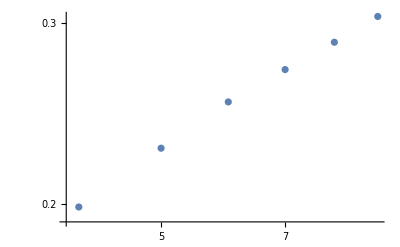

```mathematica
ListLogLogPlot@Table[{n, data1[n][[3, 2]]}, {n, 4, 9}]
```

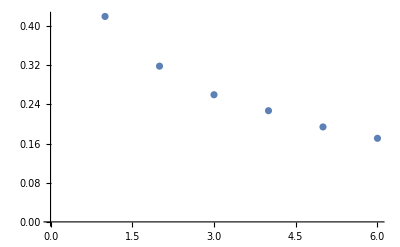

```mathematica
ListPlot@Table[(data1[n][[3, 3]])/(data1[n][[3, 2]]), {n, 4, 9}]
```

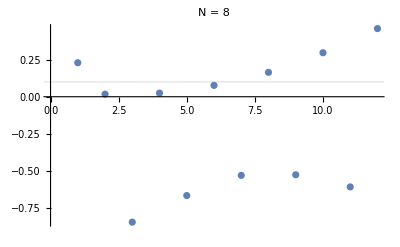

```mathematica
With[{$N = 8}, ListPlot[((#["Uncertainty"])/(#["Value"]))&/@Around/@(data2[$N][[All, 2;;]]ᵀ),
GridLines->{None, {0.1}},
PlotLabel->"N = "<>ToString@$N
]]
```

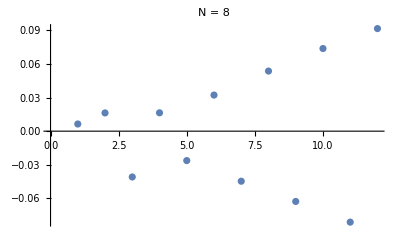

```mathematica
With[{$N = 8}, ListPlot[((#["Uncertainty"])/(#["Value"]))&/@Around/@(data3[$N][[All, 2;;]]ᵀ),
GridLines->{None, {0.1}},
PlotLabel->"N = "<>ToString@$N
]]
```

```mathematica
kk = 5;
Do[
randmat[$N] = Partition[(# - 1/($N)IdentityMatrix[$N]Tr[#])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√($N)), $N], $K*10000], $K];
σtrX1X2[$N] = StandardDeviation@Chop[Tr[#[[1]].#[[2]]]&/@randmat[$N]];
α1[$N] = (($N)^2-1)/($N data1[$N][[kk, 2]]);
α2[$N] = ((data2[$N][[kk, 3]])/σtrX1X2[$N])^-1;
α3[$N] = ($K(($N)^2-1))/($N data3[$N][[kk, 2]]);

randmat[$N] = Partition[(# - 1/($N)IdentityMatrix[$N]Tr[#])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√(α1[$N] $N)), $N], $K*100000], $K];
trX1sq[$N] = Chop[Tr[#[[1]].#[[1]]]&/@randmat[$N]];
σ = StandardDeviation@trX1sq[$N];
datas1[$N] = Join[{Mean@trX1sq[$N], σ}, Table[CentralMoment[trX1sq[$N], m], {m, 3, 12}]];

trX1X2[$N] = Chop[Tr[#[[1]].#[[2]]]&/@randmat[$N]];
σ = StandardDeviation@trX1X2[$N];
datas2[$N] = Join[{Mean@trX1X2[$N], σ}, Table[CentralMoment[trX1X2[$N], m], {m, 3, 12}]];

trXiXi[$N] = Chop[Sum[Tr[#[[i]].#[[i]]], {i, 1, $K}]&/@randmat[$N]];
σ = StandardDeviation@trXiXi[$N];
datas3[$N] = Join[{Mean@trXiXi[$N], σ}, Table[CentralMoment[trXiXi[$N], m], {m, 3, 12}]];
, {$N, 4, 9}];
```

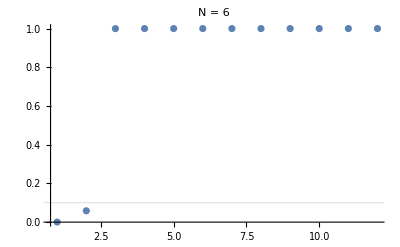

```mathematica
With[{$N = 6}, ListPlot[Abs[(datas1[$N]-data1[$N][[kk, 2;;]])/(data1[$N][[kk, 2;;]])],
PlotRange->All,
GridLines->{None, {0.1}},
PlotLabel->"N = "<>ToString@$N
]]
```

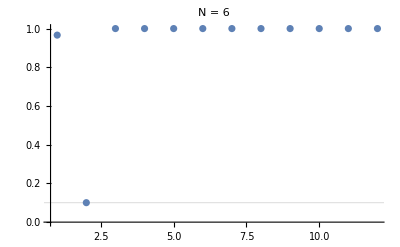

```mathematica
With[{$N = 6}, ListPlot[Abs[(datas2[$N]-data2[$N][[kk, 2;;]])/(data2[$N][[kk, 2;;]])],
PlotRange->All,
GridLines->{None, {0.1}},
PlotLabel->"N = "<>ToString@$N
]]
```

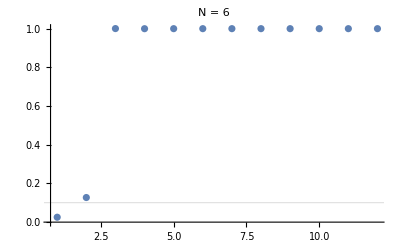

```mathematica
With[{$N = 6}, ListPlot[Abs[(datas3[$N]-data3[$N][[kk, 2;;]])/(data3[$N][[kk, 2;;]])],
PlotRange->All,
GridLines->{None, {0.1}},
PlotLabel->"N = "<>ToString@$N
]]
```

```mathematica
data3[6][[kk, 2;;]]
```

{2.14282,0.190625,-1.58473,12.8477,-68.1062,590.271,-4288.51,39349.6,-320510.,2.96835×10^6,-2.55136×10^7,2.3574×10^8}

```mathematica
datas3[6]
```

{2.0884,0.16638,0.000705333,0.00231597,0.000188185,0.000325602,0.0000522325,0.0000646349,0.0000163996,0.0000166372,5.87044×10^-6,5.28311×10^-6}

```mathematica
StandardDeviation[#]/Mean[#]&/@
```